```mathematica
Remove["Global`*"];
```

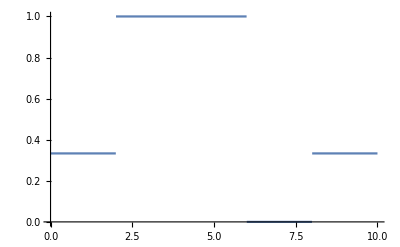

```mathematica
w=Piecewise[{{1,logk>2&&logk<6},{0,logk>6&&logk<8}},1/3];
beta=-2(1-3*w)/(1+3*w);
Plot[w,{logk,0,10}]
```

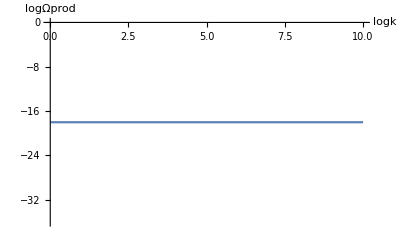

```mathematica
init=-18;
Plot[init,{logk,0,10},AxesLabel->{logk,logΩprod}]
```

```mathematica
Ω[x_,a_]:=init+UnitStep[x-(10-a)]*Integrate[beta,{logk,10-a,x},Assumptions->{x,a}∈Reals];
```

```mathematica
Animate[Plot[Ω[x,a],{x,0,10},AxesLabel->{logk,logΩ}],{a,0,10},AnimationRunning->False]
```